```mathematica
f1[thetah_,theta0_]:=((3 Tan[phi] Cos[thetah]+Sin[thetah])(Exp[3(thetah-theta0)Tan[phi]] )-(3 Tan[phi] Cos[theta0]+Sin[theta0]))/(3 (1 + 9 Tan[phi]^2));
hr0[thetah_,theta0_]:=(Sin[thetah]Exp[(thetah-theta0)Tan[phi]] -Sin[theta0]);
(*lr0[thetah_,theta0_]:=Cos[theta0]-Cos[thetah ]Exp[(thetah-theta0)Tan[phi]];*)
lr0[thetah_,theta0_]:=Sin[thetah-theta0]/Sin[thetah]-(Sin[thetah+beta]/(Sin[thetah]Sin[beta ]))(Exp[(thetah-theta0)Tan[phi]] Sin[thetah]-Sin[theta0]);
(*lr0[thetah_,theta0_]:=Cos[theta0]-hr0[thetah,theta0]Cos[beta];*)
(*lr0[thetah_,theta0_]:=Cos[theta0]-hr0[thetah,theta0]Tan[Pi/2-beta];*)

f2[thetah_,theta0_]:=1/6 lr0[thetah,theta0](2 Cos[theta0]-lr0[thetah,theta0])Sin[theta0];
(*f3[thetah_,theta0_]:=1/3 hr0[thetah,theta0]Sin[beta]Cos[thetah]^2 Exp[2 (thetah-theta0)Tan[phi]]*)
f3[thetah_,theta0_]:=(1/6 Exp[ (thetah-theta0)Tan[phi]])(Sin[thetah-theta0]-lr0[thetah,theta0] Sin[thetah])(Cos[theta0]-lr0[thetah,theta0]+Cos[thetah] Exp[(thetah-theta0) Tan[phi]]);

f[thetah_,theta0_]:=(( Exp[2 (thetah-theta0)Tan[phi]]-1)(Sin[thetah]Exp[(thetah-theta0) Tan[phi]]-Sin[theta0]))/(2Tan[phi] (f1[thetah,theta0]-f2[thetah,theta0]-f3[thetah,theta0]));
```

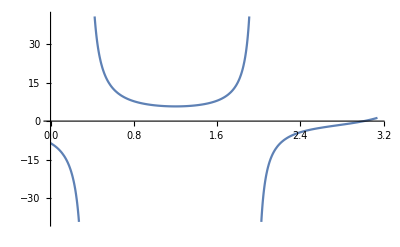

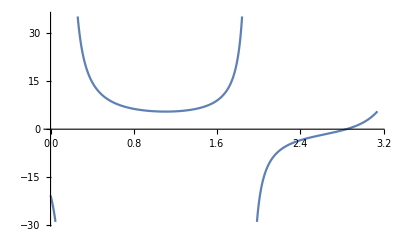

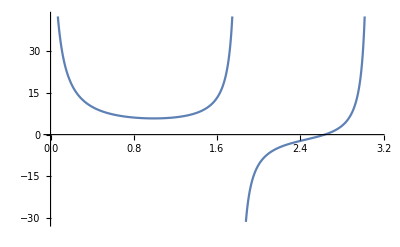

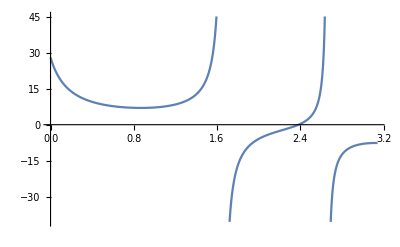

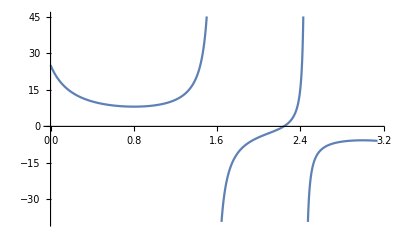

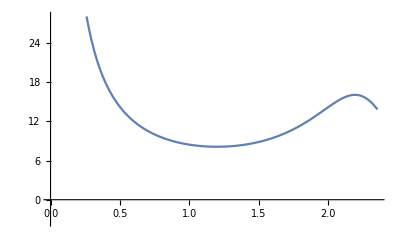

```mathematica
func=f[thetah,theta0]/.{phi->20 Pi/180,alpha->0,beta->90 Pi/180};
plot20=func/.theta0->20 Pi/180.;
plot40=func/.theta0->40 Pi/180.;
plot60=func/.theta0->60 Pi/180.;
plot80=func/.theta0->80 Pi/180.;
plot90=func/.theta0->90 Pi/180.;
Plot[plot20,{thetah,0,Pi}]
Plot[plot40,{thetah,0,Pi}]
Plot[plot60,{thetah,0,Pi}]
Plot[plot80,{thetah,0,Pi}]
Plot[plot90,{thetah,0,Pi}]
```

```mathematica
dtheta0=D[func,theta0];
dthetah=D[func,thetah];
solm=FindRoot[{dtheta0==0,dthetah==0},{theta0,1.1},{thetah,0.5}]
func/.solm
```

{theta0→0.684215,thetah→1.11011}

5.5049

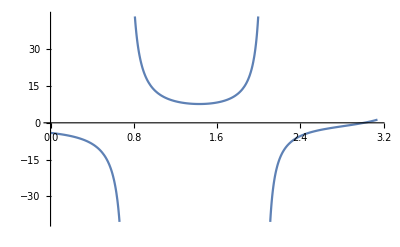

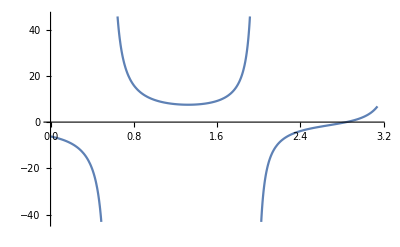

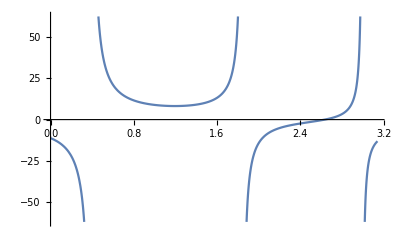

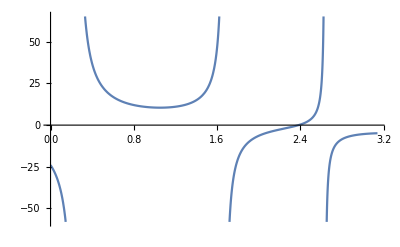

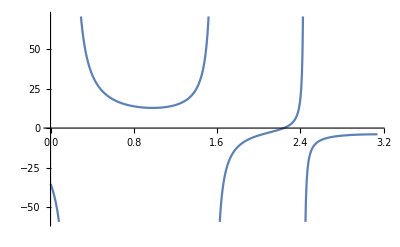

```mathematica
func=f[thetah,theta0]/.{phi->20 Pi/180,alpha->0,beta->75Pi/180};
plot20=func/.theta0->20 Pi/180.;
plot40=func/.theta0->40 Pi/180.;
plot60=func/.theta0->60 Pi/180.;
plot80=func/.theta0->80 Pi/180.;
plot90=func/.theta0->90 Pi/180.;
Plot[plot20,{thetah,0,Pi}]
Plot[plot40,{thetah,0,Pi}]
Plot[plot60,{thetah,0,Pi}]
Plot[plot80,{thetah,0,Pi}]
Plot[plot90,{thetah,0,Pi}]
```

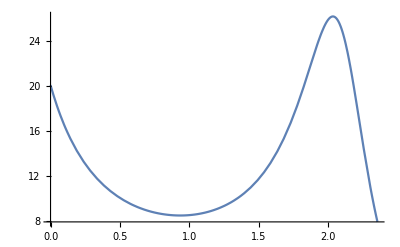

```mathematica
functhetah=func/.thetah->Pi/3;
Plot[functhetah,{theta0,0,1.5Pi/2}]
```

```mathematica
dtheta0=D[func,theta0];
dthetah=D[func,thetah];
solm=FindRoot[{dtheta0==0,dthetah==0},{theta0,0.9},{thetah,Pi/3}]
func/.solm
```

{theta0→0.60514,thetah→1.35344}

7.47672

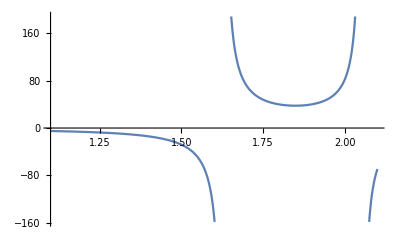

```mathematica
func=f[thetah,theta0]/.{phi->30 Pi/180,alpha->0.,beta->45Pi/180};
plot=func/.theta0->40 Pi/180.;
Plot[plot,{thetah,1.1,2.1}]
```

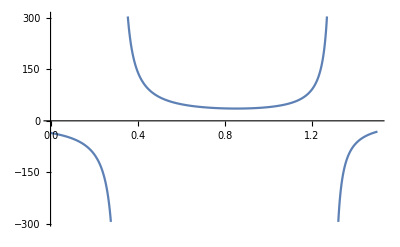

```mathematica
functhetah=func/.thetah->1.8;
Plot[functhetah,{theta0,0,1.5}]
```

```mathematica
dtheta0=D[func,theta0];
dthetah=D[func,thetah];
solm=FindRoot[{dtheta0==0,dthetah==0},{theta0,0.8},{thetah,1.8}]
func/.solm
```

{theta0→0.900171,thetah→1.77121}

35.5405

```mathematica
35.5405/20.
```

1.77703

```mathematica
40 Pi/180.
```

0.698132

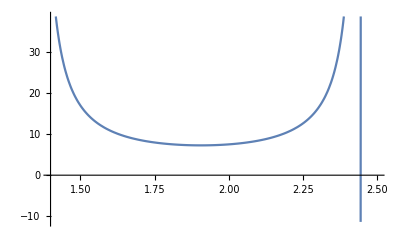

```mathematica
func=f[thetah,theta0]/.{phi-> 0.001 Pi/180,alpha->0.,beta->26.5651Pi/180};
plot=func/.theta0->40 Pi/180.;
Plot[plot,{thetah,1.4,2.5}]
```

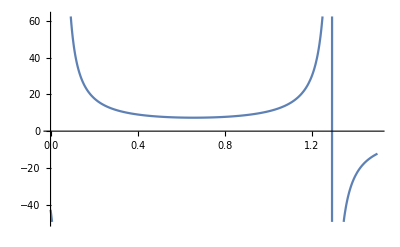

```mathematica
functhetah=func/.thetah->1.85;
Plot[functhetah,{theta0,0,1.5}]
```

```mathematica
dtheta0=D[func,theta0];
dthetah=D[func,thetah];
solm=FindRoot[{dtheta0==0,dthetah==0},{theta0,0.6},{thetah,1.8}]
func/.solm
```

{theta0→0.293185,thetah→2.22177}

6.54715

```mathematica
6.547151388581684/(20 5/23.)
```

1.50584

```mathematica
5.53/(20 5/23.)
```

1.2719

```mathematica
(*f4[th_,t0_]:=hr0[th,t0]^2 Sin[beta-betal]/(2 Sin[beta]Sin[betal])
(Cos[t0]-lr0[th,t0]-1/3 hr0[th,t0](Cot[betal]+Cot[beta]))*)
```

```mathematica
10 20/5.53
```

36.1664